```mathematica
Needs["MaTeX`"]
MaTeX["\\int\\frac{i x^2}{i+x^2}dx"]
```

-Graphics-

Potencial efectivo para V=-1/r

```mathematica
With[{l=0.2},Plot3D[-1/r^2+l^2/(2 r^2 Sin[θ]^2),{r,0,1},{θ,0,π},AxesLabel->Automatic]]
```

-Graphics3D-

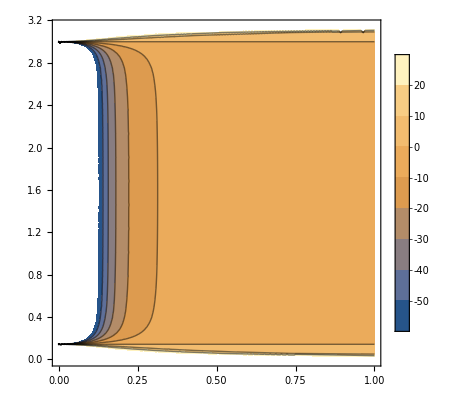

```mathematica
With[{l=0.2},ContourPlot[-1/r^2+l^2/(2 r^2 Sin[θ]^2),{r,0,1},{θ,0,π},PlotLegends->Automatic]]
```

```mathematica
l=0.2;
ti=0;
tf=30;
```

Ecuaciones de movimiento para V=-1/r

```mathematica
s=NDSolve[{vr[t]==r'[t] ,vθ[t]==θ'[t],vθ'[t]== -(2 vr[t] vθ[t])/r[t]+(l^2 Cos[θ[t]])/(r[t]^4 Sin[θ[t]]^3), vr'[t]==r[t] vθ[t]^2 +l^2/(r[t]^3 Sin[θ[t]]^2)-1/r[t]^2, vr[0]== 0,r[0]==1, vθ[0]== 1, θ[0]==π/4},{r,θ,vr,vθ},{t,ti,tf}]
```

{{r→InterpolatingFunction[…],θ→InterpolatingFunction[…],vr→InterpolatingFunction[…],vθ→InterpolatingFunction[…]}}

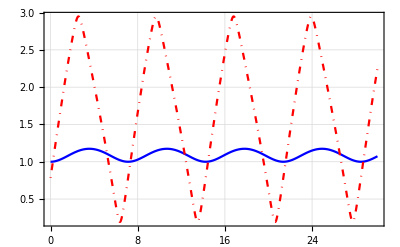

```mathematica
Plot[Evaluate[{r[t],θ[t]}/.s],{t,ti,tf}, PlotRange->All,FrameLabel->{MaTeX["t", Magnification->1.3],},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}},PlotLegends->Placed[{MaTeX["r(t)", Magnification->1.3],MaTeX["\\theta(t)", Magnification->1.3]},{Right,Top}],GridLines->Automatic]
```

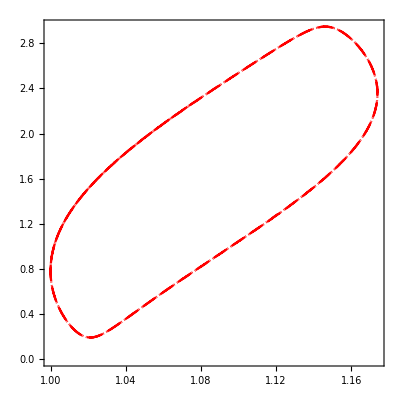

```mathematica
ParametricPlot[Evaluate[{r[t],θ[t]}/.s],{t,ti,tf},AspectRatio->1,FrameLabel->{MaTeX["r(t)", Magnification->1.3],MaTeX["\\theta(t)", Magnification->1.3]},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}}]
```

Lo mismo pero con el parámetro ϕ (llamado x aquí)

```mathematica
l=0.2;
```

```mathematica
J=NDSolve[{vvr[x]==r'[x] ,vvθ[x]==θ'[x],vvθ'[x]== (2 Cos[θ[x]] vvθ[x])/(l  Sin[θ[x]])+ Sin[θ[x]] Cos[θ[x]], vvr'[x]==r[x] vvθ[x]^2 +r[x] Sin[θ[x]]^2+2/r[x](Sin[θ[x]]^2 vvr[x]^2+r[x] Sin[θ[x]] Cos[θ[x]] vvθ[x] vvr[x])-(r[x]^2 Sin[θ[x]]^4)/l^2, vvr[0]== 0,r[0]==1, vvθ[0]== 1/2, θ[0]==π/4},{r,θ,vvr,vvθ},{x,0,2π}]
```

{{r→InterpolatingFunction[…],θ→InterpolatingFunction[…],vvr→InterpolatingFunction[…],vvθ→InterpolatingFunction[…]}}

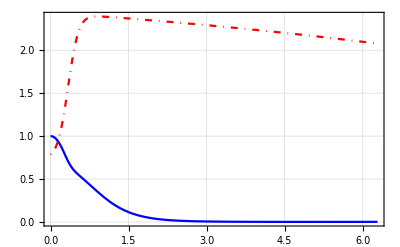

```mathematica
Plot[Evaluate[{r[ϕ],θ[ϕ]}/.J],{ϕ,0,2π}, PlotRange->All,FrameLabel->{MaTeX["\\phi", Magnification->1.3],},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}},PlotLegends->Placed[{MaTeX["r(\\phi)", Magnification->1.3],MaTeX["\\theta(\\phi)", Magnification->1.3]},{Right,Top}],GridLines->Automatic]
```

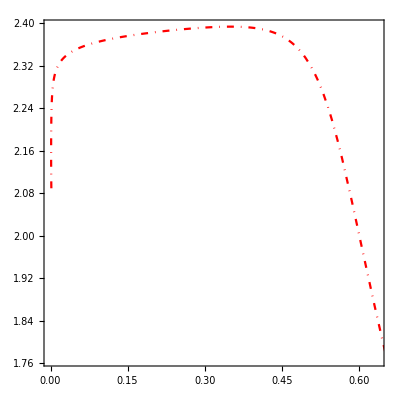

```mathematica
ParametricPlot[Evaluate[{r[ϕ],θ[ϕ]}/.J],{ϕ,0,2π},AspectRatio->1,FrameLabel->{MaTeX["r(\\phi)", Magnification->1.3],MaTeX["\\theta(\\phi)", Magnification->1.3]},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}}]
```

Potencial generalizado de Plummer Kuzmin

```mathematica
G=1;M=1;
V[r_,θ_]:= -(G M)/((r^2+a^2+b^2 +2 a (r^2 Cos[θ]^2+b^2)^(1/2))^(1/2));
Vef[r_,θ_]:=l^2/(2 r^2 Sin[θ]^2)+V[r,θ]
```

Potencial efectivo

```mathematica
With[{l=0.2,a=0.5,b=0.5},Plot3D[-(G M)/((r^2+a^2+b^2 +2 a (r^2 Cos[θ]^2+b^2)^(1/2))^(1/2))+l^2/(2 r^2 Sin[θ]^2),{r,0,1},{θ,0,π},AxesLabel->Automatic]]
```

-Graphics3D-

```mathematica
D[V[r,θ],r]//Simplify
```

(r (1+(a Cos[θ]^2)/(√(b^2+r^2 Cos[θ]^2))))/((a^2+b^2+r^2+2 a √(b^2+r^2 Cos[θ]^2))^(3/2))

```mathematica
D[V[r,θ],θ]/r^2//Simplify
```

-(a Cos[θ] Sin[θ])/(√(b^2+r^2 Cos[θ]^2) (a^2+b^2+r^2+2 a √(b^2+r^2 Cos[θ]^2))^(3/2))

Ecuaciones de movimiento para V=-(G M)/((r^2+a^2+b^2 +2 a (r^2 Cos[θ]^2+b^2)^(1/2))^(1/2))

```mathematica
l=0.2;a=0.5;b=0.5;
ti=0;
tf=25;
condin ={vr[0]== 0,r[0]==0.5, vθ[0]== 1, θ[0]==π/4};
```

```mathematica
ecs ={vr[t]==r'[t] ,vθ[t]==θ'[t], vr'[t]==r[t] vθ[t]^2 +l^2/(r[t]^3 Sin[θ[t]]^2)-(r[t] (1+(a Cos[θ[t]]^2)/(√(b^2+r[t]^2 Cos[θ[t]]^2))))/((a^2+b^2+r[t]^2+2 a √(b^2+r[t]^2 Cos[θ[t]]^2))^(3/2)),vθ'[t]== -(2 vr[t] vθ[t])/r[t]+(l^2 Cos[θ[t]])/(r[t]^4 Sin[θ[t]]^3)+(a Cos[θ[t]] Sin[θ[t]])/(√(b^2+r[t]^2 Cos[θ[t]]^2) (a^2+b^2+r[t]^2+2 a √(b^2+r[t]^2 Cos[θ[t]]^2))^(3/2))};
```

```mathematica
s=NDSolve[{ecs, condin},{r,θ,vr,vθ},{t,ti,tf}]
```

{{r→InterpolatingFunction[…],θ→InterpolatingFunction[…],vr→InterpolatingFunction[…],vθ→InterpolatingFunction[…]}}

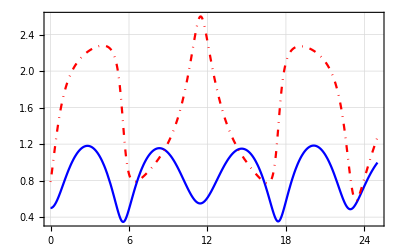

```mathematica
Plot[Evaluate[{r[t],θ[t]}/.s],{t,ti,tf}, PlotRange->All,FrameLabel->{MaTeX["t", Magnification->1.3],},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}},PlotLegends->Placed[{MaTeX["r(t)", Magnification->1.3],MaTeX["\\theta(t)", Magnification->1.3]},{Right,Top}],GridLines->Automatic]
```

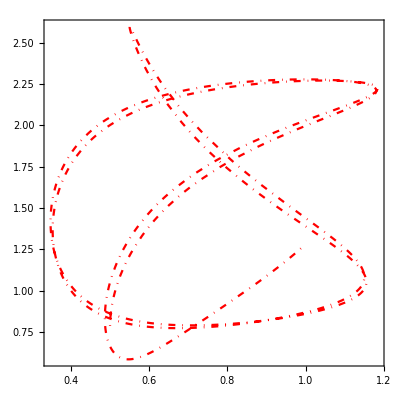

```mathematica
ParametricPlot[Evaluate[{r[t],θ[t]}/.s],{t,ti,tf},AspectRatio->1,FrameLabel->{MaTeX["r(t)", Magnification->1.3],MaTeX["\\theta(t)", Magnification->1.3]},Frame->True,FrameStyle->BlackFrame,PlotStyle->{Blue,{Red ,DotDashed}}]
```

densidad de masa

```mathematica
G=1
```

1

```mathematica
r[x_,y_,z_]:=√(x^2+y^2+z^2);
θ[x_,y_,z_]:=ArcCos[z/√(x^2+y^2+z^2)] ;
```

```mathematica
dens[a_,b_,r_,θ_]:=((b^2 M)/(4 π)) ((a r^2 Sin[θ]^2+ (a+3 (r^2 Cos[θ]^2+b^2)^(1/2))(a+ (r^2 Cos[θ]^2+b^2)^(1/2))^2)/(r^2+a^2+b^2 +2 a (r^2 Cos[θ]^2+b^2)^(1/2))^(5/2))
```

```mathematica
Laplacian[V[r,θ],{r,θ,ϕ},"Spherical"]/(4π)//Simplify
```

(b^2 G M (2 a^3+14 a b^2+8 a r^2+10 a^2 √(b^2+r^2 Cos[θ]^2)+6 b^2 √(b^2+r^2 Cos[θ]^2)+3 r^2 √(b^2+r^2 Cos[θ]^2)+3 r^2 Cos[θ]^2 (2 a+√(b^2+r^2 Cos[θ]^2))-3 r^2 (2 a+√(b^2+r^2 Cos[θ]^2)) Sin[θ]^2))/(8 π (b^2+r^2 Cos[θ]^2)^(3/2) (a^2+b^2+r^2+2 a √(b^2+r^2 Cos[θ]^2))^(5/2))

```mathematica
dens[a_,b_,r_,θ_]:= (b^2 G M (2 a^3+14 a b^2+8 a r^2+10 a^2 √(b^2+r^2 Cos[θ]^2)+6 b^2 √(b^2+r^2 Cos[θ]^2)+3 r^2 √(b^2+r^2 Cos[θ]^2)+3 r^2 Cos[θ]^2 (2 a+√(b^2+r^2 Cos[θ]^2))-3 r^2 (2 a+√(b^2+r^2 Cos[θ]^2)) Sin[θ]^2))/(8 π (b^2+r^2 Cos[θ]^2)^(3/2) (a^2+b^2+r^2+2 a √(b^2+r^2 Cos[θ]^2))^(5/2))
```

```mathematica
M=1; G=1
```

1

1

```mathematica
DensityPlot3D[dens[0.5,0.5,r[x,y,z],θ[x,y,z]],{x,y,z}∈Ball[{0,0,0},10],PlotLegends->Automatic,AxesLabel->Automatic ,PlotTheme->"Marketing"]
```

-Graphics3D-

```mathematica
DensityPlot3D[dens[1,0,r[x,y,z],θ[x,y,z]],{x,y,z}∈Ball[{0,0,0},10],PlotLegends->Automatic,AxesLabel->Automatic ,PlotTheme->"Marketing", ClipPlanes->{0,1,0,0}]
```

-Graphics3D-

```mathematica
DensityPlot3D[dens[0,1,r[x,y,z],θ[x,y,z]],{x,y,z}∈Ball[{0,0,0},10],PlotLegends->Automatic,AxesLabel->Automatic ,PlotTheme->"Marketing"]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[Table[dens[i,j,r,θ],{i,0,1,0.5},{j,0,1,0.5}]], {r,0,10},{θ,0,π}]
```

-Graphics3D-